# Student-T NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## definitions and derivations

```mathematica
ST`D[u_,α_,γ_]:=((1+(1-u^2)/(u^2 α^2 (-1+γ)))^-γ)/(π u^4 α^2)HeavisideTheta[u]
```

```mathematica
ST`σ[u_,α_,γ_]:=u/2+(α (1-u^2/((-1+u^2) α^2 (-1+γ)))^(3/2-γ) √((1-u^2) (-1+γ)) Gamma[-3/2+γ])/(2 √π Gamma[-1+γ])+(u^2 Gamma[-1/2+γ] Hypergeometric2F1[1/2,-1/2+γ,3/2,u^2/((-1+u^2) α^2 (-1+γ))])/(√π α √((1-u^2) (-1+γ)) Gamma[-1+γ])
```

```mathematica
ST`Λ[u_,α_,γ_]:=1/(4 √π u Gamma[-1+γ])(2 α^(-2+2 γ) (u^2-(-1+u^2) α^2 (-1+γ))^(3/2-γ) ((1-u^2) (-1+γ))^(-1+γ)+(-1)^-γ u (-3+2 γ) Beta[((-1+u^2) α^2 (-1+γ))/u^2,-1+γ,3/2-γ]) Gamma[-3/2+γ]
```

```mathematica
(1+ST`Λ[u,α,γ])u==ST`σ[u,α,γ]/.γ->3/.u->1/2/.α->1/3//FullSimplify
```

True

```mathematica
ST`Λ[u,α,γ]u==ST`σ[-u,α,γ]/.γ->3/.u->1/2/.α->1/3//FullSimplify
```

True

```mathematica
FullSimplify[ST`Λ[u,u/(√(1-u^2) x),γ],Assumptions->0<u<1&&x>0&&γ>3/2]
```

((-1+γ)^γ Gamma[-3/2+γ] ((2 (-1+x^2+γ)^(3/2-γ))/Gamma[γ]-(x^(3-2 γ) (-3+2 γ) Hypergeometric2F1Regularized[-1+γ,-1/2+γ,γ,(1-γ)/x^2])/(-1+γ)))/(4 √π x)

### shape invariant f(x)

```mathematica
FullSimplify[ST`D[u,α,γ] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0&&α>2]
```

(((-1+γ)/(-1+x^2+γ))^γ)/π

### Relationship to Beckmann NDF:

```mathematica
Integrate[PDF[GammaDistribution[γ-1,1]][αB]Beckmann`D[u,α √((γ-1)/αB)],{αB,0,Infinity},Assumptions->α>0&&0<u<1&&γ>3/2]
```

((1+(1-u^2)/(u^2 α^2 (-1+γ)))^-γ)/(π u^4 α^2)

### height field normalization

```mathematica
Integrate[2Pi u ST`D[u,α,γ],{u,0,1},Assumptions->0<α&&γ>3/2]
```

1

### distribution of slopes

```mathematica
FullSimplify[ST`D[1/(√(p^2+q^2+1)),α,γ](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

(α^(-2+2 γ) (p^2+q^2+α^2 (-1+γ))^-γ (-1+γ)^γ)/π

```mathematica
ST`P22[p_,q_,α_,γ_]:=(α^(-2+2 γ) (p^2+q^2+α^2 (-1+γ))^-γ (-1+γ)^γ)/π
```

```mathematica
Integrate[ST`P22[p,q,α,γ],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1&&γ>2]
```

1

```mathematica
Integrate[ST`P22[p,q,α,γ],{q,-Infinity,Infinity},Assumptions->0<α<1&&γ>2]
```

ConditionalExpression[(α^(-2+2 γ) (p^2+α^2 (-1+γ))^(1/2-γ) (-1+γ)^γ Gamma[-1/2+γ])/(√π Gamma[γ]),α^2 γ+Re[p^2]>α^2]

```mathematica
ST`P2[p_,α_,γ_]:=(α^(-2+2 γ) (p^2+α^2 (-1+γ))^(1/2-γ) (-1+γ)^γ Gamma[-1/2+γ])/(√π Gamma[γ])
```

### compare σ to delta integral:

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

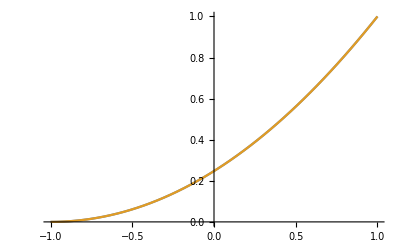

```mathematica
With[{α=.7,γ=3},
Plot[{
 Quiet[NIntegrate[ST`D[ui,α,γ]Delta`σ[u,ui],{ui,0,1}]],
ST`σ[u,α,γ]
},{u,-1,1}]
]
```